# Sin[x]&Sin[y]

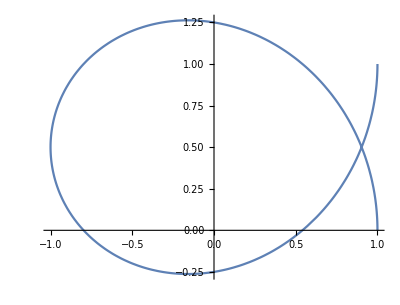

```mathematica
Clear[x,y]
x[v_]:=Cos[v]
y[v_]:=Sin[v]+v/(2*Pi)
ParametricPlot[{x[v],y[v]},{v,0,2π}]
```

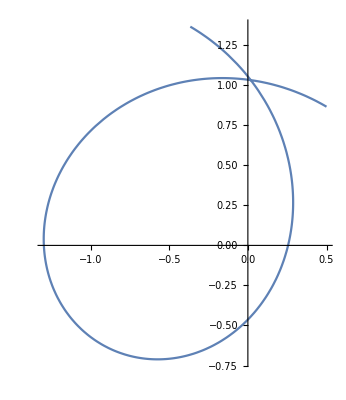

```mathematica
ParametricPlot[(x[v]+I y[v])E^(I π/3)//ReIm,{v,0,2π}]
```

```mathematica
∀_(v,0<v<2π)∃_(v2,0<v2<2π&&v!=v2)x[v]==x[v2]&&y[v]+y[v2]==1
```

∀_(v,0<v<2 π)∃_(v2,0<v2<2 π&&v≠v2)Cos[v]==Cos[v2]&&v/(2 π)+v2/(2 π)+Sin[v]+Sin[v2]==1

```mathematica
Plot3D[Sin[x]+Sin[y],{x,-10,10},{y,-10,10},PlotPoints->50,PlotLegends->"Expressions"]
```

-Graphics3D-

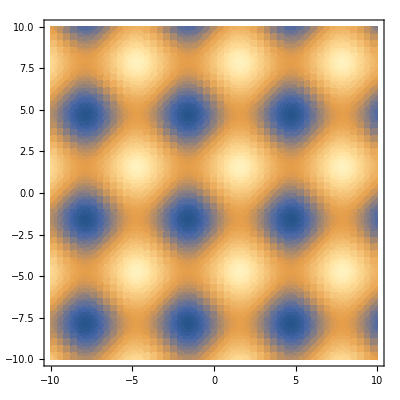

```mathematica
DensityPlot[Sin[x]+Sin[y],{x,-10,10},{y,-10,10},PlotPoints->50]
```

```mathematica
ContourPlot[Sin[x]+Sin[y],{x,-10,10},{y,-10,10},PlotPoints->50]
```

-Graphics-

```mathematica
Manipulate[ContourPlot[Sin[x]+Sin[y]==v,{x,-10,10},{y,-10,10},PlotPoints->50],{{v,0,"高度"},-2,2}]
```

```mathematica
t=Table[Sin[x]~s~ Sin[y],{s,{Plus,Subtract,Times,Divide}}]
Plot3D[t,{x,-10,10},{y,-10,10},PlotPoints->50,PlotLegends->"Expressions"]
Plot3D[#,{x,-10,10},{y,-10,10},PlotPoints->50]&/@t
```

{Sin[x]+Sin[y],Sin[x]-Sin[y],Sin[x] Sin[y],Csc[y] Sin[x]}

-Graphics3D-

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

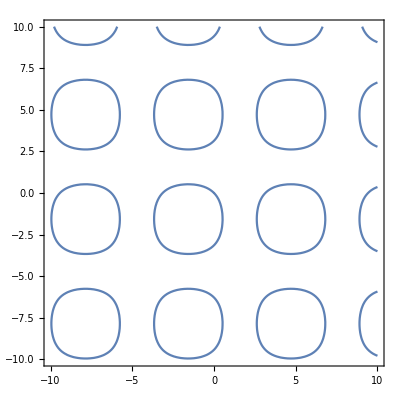

```mathematica
ContourPlot[Sin[x]+Sin[y]==Sin[x]Sin[y],{x,-10,10},{y,-10,10},PlotPoints->50]
```

```mathematica
Plot3D[Sin[x^2]+Sin[y^2],{x,-10,10},{y,-10,10},PlotPoints->50]
```

-Graphics3D-

```mathematica
DensityPlot[Sin[x^2]+Sin[y^2],{x,-10,10},{y,-10,10},PlotPoints->50]
```

-Graphics-

```mathematica
ContourPlot[Sin[x^2]+Sin[y^2],{x,-10,10},{y,-10,10}]
```

-Graphics-

```mathematica
Manipulate[ContourPlot[Sin[x^2]+Sin[y^2]==v,{x,-10,10},{y,-10,10},PlotPoints->50,ContourStyle->RandomColor[]],{{v,0,"高度"},-2,2}]
```